y''[x]/(√(1+y'[x]^2))==0

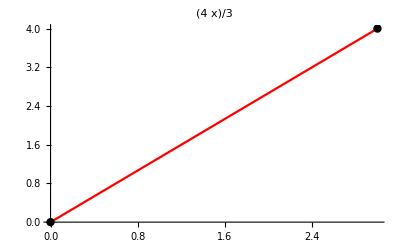

```mathematica
<<VariationalMethods`
firstF[x_,y_,yd_]:=Sqrt[1+yd^2];
firstAE=FullSimplify[EulerEquations[firstF[x,y[x],y'[x]],y[x],x]]
firstY[x_]=DSolveValue[{firstAE,y[0]==0,y[3]==4},y[x],x];
firstPlot=Show[
Plot[firstY[x],{x,0,3},PlotLabel->firstY[x],PlotStyle->Red],
Graphics[{PointSize[0.015],Point[{{0,0},{3,4}}]}]
]

(*masodik probalkozas*)
Manipulate[
firstY[x_]=DSolveValue[{firstAE,y[a[[1]]]==a[[2]],y[b[[1]]]==b[[2]]},y[x],x];
firstPlot=Show[
Plot[firstY[x],{x,0,3},PlotLabel->firstY[x],PlotStyle->Red],
Graphics[{PointSize[0.015],Point[{a,b}]}]
],
{{a,{0,0}},Locator}, {{b, {3,4}}, Locator}
]
```

```mathematica
(*harmadik probalkozas*)
Manipulate[
firstY[x_]=DSolveValue[{firstAE,y[a[[1]]]==a[[2]],y[b[[1]]]==b[[2]]},y[x],x];
firstPlot=Show[
Plot[firstY[x],{x,0,3},PlotLabel->firstY[x],PlotStyle->Red],
Graphics[{PointSize[0.015],Point[{a,b}]}]
],
{{a,{0,0}},Locator}, {{b, {3,4}}, Locator}
]
```

```mathematica
(*3. Feladat*)
{x0,y0}={0,0};
{x1,y1}={2,-1};
g=9.81;

xgamma=Interpolation[{{0,0},{0.1,0.20920779025264685},{0.2,0.4173143292731987},{0.30000000000000004,0.6433438583238918},{0.4,0.8454464723174622},{0.5,1.0483595257521727},{0.6,1.2810417741293318},{0.7000000000000001,1.4324102465866777},{0.8,1.670551881612325},{0.9,1.849854247738263},{1,2}}];

ygamma=Interpolation[{{0,0},{0.1,-0.09830706451409998},{0.2,-0.18597952682698346},{0.30000000000000004,-0.2922175903934895},{0.4,-0.3758268370548955},{0.5,-0.4246485331888572},{0.6,-0.5607198627905221},{0.7000000000000001,-0.6227727433112606},{0.8,-0.7024793058085955},{0.9,-0.8655440671292081},{1,-1}}];

Manipulate[
plotPointsAB=Graphics[{
{PointSize[0.015],Point[{{x0,y0},{x1,y1}}]},
Text[Style["A(0,0)",FontSize->14],{0.2,0.1}],
Text[Style["B(2,-1)",FontSize->14],{2.1,-0.9}]
},Axes->True
,AxesStyle->Arrowheads[{0.0,0.03}]];
plotGamma=ParametricPlot[{xgamma[t],ygamma[t]},{t,0,1},PlotStyle->Purple];
Show[plotPointsAB,plotGamma],
{x0, 0, 2}, {y0, 0, 2}, {x1, 2, 4}, {y1, 0, -2}
]
```

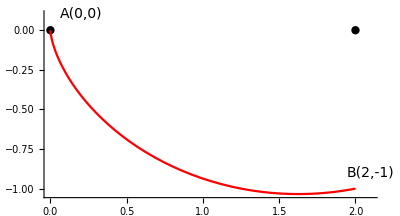

```mathematica
(*Piros Ciklois*)
{bcX,bcY}=Module[{x,y,xbc,ybc,wok,cok,dok},
x[u_]:=c*w*u-c/2*Sin[2*w*u]+d;
y[u_]:=c/2-c/2*Cos[2*w*u];
{{wok,cok,dok}}={w,c,d}/.NSolve[{x[0]==x0,y[0]==y0,x[1]==x1,y[1]==y1},{c,w,d},Reals];
xbc[t_]:=x[t]/.{w->wok,c->cok,d->dok};
ybc[t_]:=y[t]/.{w->wok,c->cok,d->dok};
{xbc,ybc}
];
bcPlot=ParametricPlot[{bcX[t],bcY[t]},{t,0,1},PlotStyle->Red];
Show[plotPointsAB, bcPlot]
```

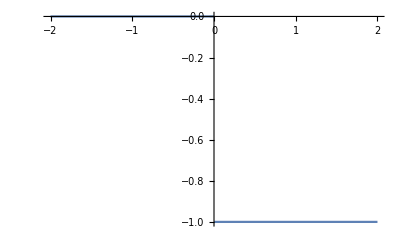

```mathematica
(*Zold gorbe*)
Plot[Piecewise[{{-1,x>0},{x,x=0}}],{x,-2,2}]
```

```mathematica
(*Kek gorbe*)
kekGorbe = Graphics[{Blue, Line[{{x0,y0}, {x1, y1}}]}];
```

```mathematica
(*Narancssarga gorbe*)
narancsGorbe = Plot[0.25(x-x1)^2+y1,{x,0,2},PlotStyle->Orange];
```

```mathematica
(*Zold gorbe2*)
zoldGorbe=Show[Graphics[{Green,Line[{{0, 0}, {0, -1}}]}], Graphics[{Green,Line[{{0, -1},{2, -1}}]}]];
```